# “Hump-backed plateau”

```mathematica
<<"/Users/gianmicheleinnocenti/Desktop/parton-shower-simulator/Kernel/PartonShowerMCFull.wl"
```

Mean multiplicty=5.09601

Mean multiplicty quarks =1.316

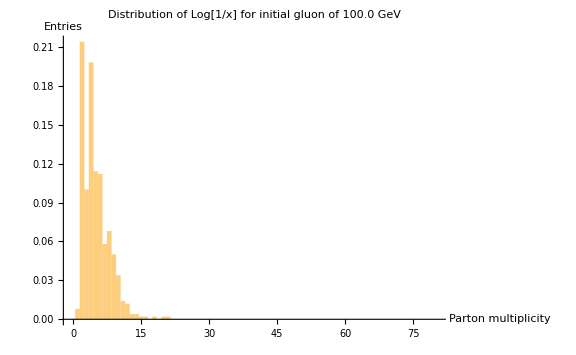

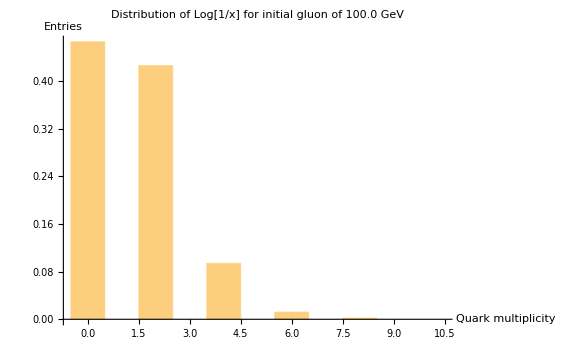

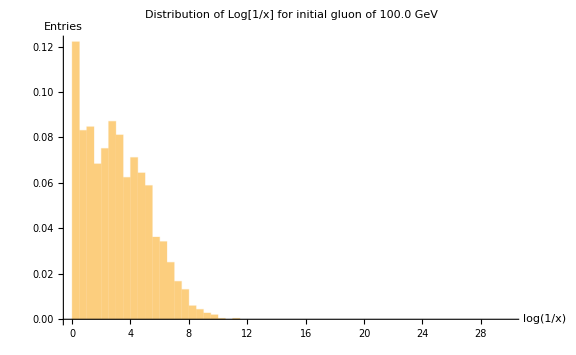

```mathematica
Off[RandomReal::precw];
Off[Greater::nord];
Off[LessEqual::nord];
Off[FindRoot::cvmit];
Off[FindRoot::frmp];
Off[Part::partd];
Off[General::stop];

SeedRandom[1234];RandomReal[];
maxevents= 500;
ptinitial=100.;
ptcutoff=1.;
descendtot ={};
zvaluestot= {};
nmultiplicitytot= {};
nmultiplicityquarkstot= {};
nquarkstot = {};
For[i=0, i<maxevents,i++,
(*Print["Event id = ",i];*)
Clear[descendentevent,zvaluesevent]; 
descendentevent = ShowerFixedUrs[ptinitial,ptcutoff,SudakovPgtoggvacuumLT, SudakovPgtoqqbarvacuumLT,PgtoggvacuumNT,PgtoqqbarvacuumLT,0,200];
zvaluesevent = Table[descendentevent[[jendex]][[3]],{jendex,Length[descendentevent]}];
nquarks=Count[descendentevent[[;;,2]],"q"];
AppendTo[descendtot,descendentevent];
AppendTo[zvaluestot,zvaluesevent];
AppendTo[nmultiplicitytot,Length[descendentevent]];
AppendTo[nmultiplicityquarkstot,nquarks];
]
meannquarks = Mean[nmultiplicityquarkstot]*1.000001;
meanmult = Mean[nmultiplicitytot]*1.000001;
Print["Mean multiplicty=", meanmult];
Print["Mean multiplicty quarks =", meannquarks];

Histogram[nmultiplicitytot,{-0.5,80.5,1.},"Probability", AxesLabel->{HoldForm["Parton multiplicity"],HoldForm[Entries]}, PlotLabel->StringTemplate["Distribution of Log[1/x] for initial gluon of `1` GeV"][ptinitial],
LabelStyle->{FontFamily->"Helvetica", 12, GrayLevel[0]},ImageSize->Large]
Histogram[nmultiplicityquarkstot,{-0.5,10.5,1.},"Probability", AxesLabel->{HoldForm["Quark multiplicity"],HoldForm[Entries]}, PlotLabel->StringTemplate["Distribution of Log[1/x] for initial gluon of `1` GeV"][ptinitial],
LabelStyle->{FontFamily->"Helvetica", 12, GrayLevel[0]},ImageSize->Large]
Histogram[Log[1/Flatten[zvaluestot]],{0.,30.,0.5},"Probability", AxesLabel->{HoldForm[Log[1/x]],HoldForm[Entries]}, PlotLabel->StringTemplate["Distribution of Log[1/x] for initial gluon of `1` GeV"][ptinitial],
LabelStyle->{FontFamily->"Helvetica", 12, GrayLevel[0]},ImageSize->Large]
```